```mathematica
data={ν->0.3,Yp->200*^9,EfBD->200*^9,ϵp->4.5*8.85*^-12,ϵf->80*8.85*^-12,EBDp->1*^-3,EBDf->1*^-3,l0->25*^-6,w->1,tp0->25*^-6}
```

{ν→0.3,Yp→200000000000,EfBD→200000000000,ϵp→3.9825×10^-11,ϵf→7.08×10^-10,EBDp→1/1000,EBDf→1/1000,l0→1/40000,w→1,tp0→1/40000}

```mathematica
solϵ1=Solve[√((x/2)^2+l0^2)==l0(1+ϵ1),ϵ1][[1]]//FullSimplify
```

{ϵ1→-1+(√(4 l0^2+x^2))/(2 l0)}

```mathematica
eqstrain={ϵ1==1/Y(σ1-ν(σ2+σ3)),ϵ2==1/Y(σ2-ν(σ1+σ3)),ϵ3==1/Y(σ3-ν(σ1+σ2))};
eqstrain=eqstrain/.σ3->0/.ϵ2->0
```

{ϵ1==(σ1-ν σ2)/Y,0==(-ν σ1+σ2)/Y,ϵ3==-(ν (σ1+σ2))/Y}

```mathematica
soldef=Solve[eqstrain,{σ1,σ2,ϵ3}][[1]]//FullSimplify
```

{σ1→-(Y ϵ1)/(-1+ν^2),σ2→-(Y ϵ1 ν)/(-1+ν^2),ϵ3→(ϵ1 ν)/(-1+ν)}

```mathematica
soldef[[3]]/.solϵ1
```

ϵ3→((-1+(√(4 l0^2+x^2))/(2 l0)) ν)/(-1+ν)

```mathematica
dA=w(1+ϵ1)
```

w (1+ϵ1)

```mathematica
tp=tp0 (1+ϵ3);
```

```mathematica
tf=((x/2-2 tp)(l0-ξ))/l0;
```

```mathematica
dCp=(dA ϵp)/tp
dCf=(dA ϵf)/tf
```

(w (1+ϵ1) ϵp)/(tp0 (1+ϵ3))

(l0 w (1+ϵ1) ϵf)/((x/2-2 tp0 (1+ϵ3)) (l0-ξ))

```mathematica
dC=(2/dCf+2/dCp)^-1
```

1/((2 tp0 (1+ϵ3))/(w (1+ϵ1) ϵp)+(2 (x/2-2 tp0 (1+ϵ3)) (l0-ξ))/(l0 w (1+ϵ1) ϵf))

```mathematica
CC=Integrate[dC,ξ]
CC=(CC/.ξ->l0)-(CC/.ξ->0)//Simplify
```

-(l0 w (1+ϵ1) ϵf Log[2 l0 tp0 (1+ϵ3) (ϵf-2 ϵp)+l0 x ϵp-x ϵp ξ+4 tp0 (1+ϵ3) ϵp ξ])/(-4 tp0+x-4 tp0 ϵ3)

(l0 w (1+ϵ1) ϵf (Log[2 l0 tp0 (1+ϵ3) ϵf]-Log[2 l0 tp0 (1+ϵ3) (ϵf-2 ϵp)+l0 x ϵp]))/(-x+4 tp0 (1+ϵ3))

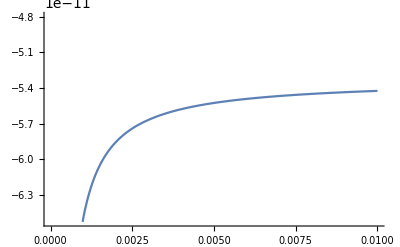

```mathematica
Plot[CC/.soldef/.solϵ1/.data,{x,0,0.01}]
```

```mathematica
Integrate[dC,ξ]//FullSimplify
```

(l0 w (1+ϵ1) ϵf Log[2 l0 tp0 (1+ϵ3) (ϵf-2 ϵp)+l0 x ϵp-x ϵp ξ+4 tp0 (1+ϵ3) ϵp ξ])/(-x+4 tp0 (1+ϵ3))